```mathematica
ClearAll["Global`*"];
```

```mathematica
dataStandingVariation=Import[NotebookDirectory[]<>"../Data/"<>"Table_standing_variants.txt","CSV"];
```

```mathematica
dataWaitingTimeSelfing=Import[NotebookDirectory[]<>"../Data/"<>"Table_MGWP_WaitingTime_Selfing.txt","CSV"];
```

## Waiting times till rescue under cross- and self-pollination

### Parameters constant under different levels of self-pollination

#### Parameters of the model

```mathematica
b=0.9 140;
dZ=0.35;
gZ = 0.2;
f=0.9 13000;
dS=0.94;
c=0.3;
kc=0.5;
cr = {0,kc c,c};
```

```mathematica
T=b(1-dZ)gZ;
S = (1-cr)f(1-dS);
```

```mathematica
g = 0.3;
dB=0.48;
μ=10^-8;
hl=0.998;
ht=0.985;
kh=0.5;
hL = {hl,(1-kh) hl, 0};
hT = {ht,(1-kh) ht, 0};
```

```mathematica
A=10^4;
densSeeds=80;
densPlants=1;
nP=A densPlants;
nB=A densSeeds;
```

```mathematica
M={(1-μ)^2 {{1,0.5,0},{0.5,0.25,0},{0,0,0}}+μ(1-μ) {{0,0.5,1},{0.5,0.5,0.5},{1,0.5,0}}+μ^2{{0,0,0},{0,0.25,0.5},{0,0.5,1}},2 μ (1-μ) {{1,0.5,0},{0.5,0.25,0},{0,0,0}}+((1-μ)^2 +μ^2) {{0,0.5,1},{0.5,0.5,0.5},{1,0.5,0}}+2 μ (1-μ){{0,0,0},{0,0.25,0.5},{0,0.5,1}},μ^2 {{1,0.5,0},{0.5,0.25,0},{0,0,0}}+μ {{0,0.5,1},{0.5,0.5,0.5},{1,0.5,0}}+{{0,0,0},{0,0.25,0.5},{0,0.5,1}}}//N;
```

#### Parameters of the offspring distributions

```mathematica
α=(1-dB) g (1-hL);
β=(1-dB) (1-g);
γ=(dB+(1-dB) g hL);
```

### Waiting time distribution for a cross-pollinating population

```mathematica
nMax=50;
```

#### Proportion of self-pollination

```mathematica
p=0;
```

#### Parameters of the offspring distributions

```mathematica
λ[i_,j_]:=(M[[j,i,i]] p S[[i]]+M[[j,i,1]] (1-p)(S[[i]]+(1-KroneckerDelta[1,i]) S[[1]]))g (1-hL[[j]])+KroneckerDelta[j,i]T(1-hT[[j]]);
λm[i_,j_]:=(M[[j,i,i]] p S[[i]]+M[[j,i,1]] (1-p)(S[[i]]+(1-KroneckerDelta[1,i]) S[[1]]))(1-g);
```

#### Offspring generating function

```mathematica
G[s_]:={Exp[λ[1,1] (s[[1]]-1)+ λ[1,2] (s[[2]]-1)+ λ[1,3] (s[[3]]-1)+ λm[1,1] (s[[4]]-1)+ λm[1,2] (s[[5]]-1)+ λm[1,3] (s[[6]]-1)],0,0,α[[1]]s[[1]]+β s[[4]]+γ[[1]],α[[2]]s[[2]]+β s[[5]]+γ[[2]],α[[3]]s[[3]]+β s[[6]] +γ[[3]]}
```

#### Standing genetic variation

```mathematica
pos=Position[dataStandingVariation⟦All,{1,2}⟧,{p,c}]⟦1,1⟧;
v = {dataStandingVariation[[pos]][[3]],dataStandingVariation[[pos]][[4]],dataStandingVariation[[pos]][[5]]};
```

#### Waiting time till the first resistant plant establishes on the field

```mathematica
Π[n_]:=Nest[G[#]&,{1,0,0,1,1,1},n];
```

```mathematica
F[n_]:=1-Exp[nP (v[[1]] (Π[n][[1]]-1)-v[[2]]-v[[3]])+nB(v[[1]] (Π[n][[4]]-1)+v[[2]] (Π[n][[5]]-1)+v[[3]] (Π[n][[6]]-1))]
```

```mathematica
P1=Prepend[Table[F[n]-F[n-1],{n,1,nMax}],1-Exp[-nP (v[[2]]+v[[3]])]];
```

```mathematica
F1=Table[F[n],{n,0,nMax}];
```

### Waiting time distribution for a self-pollinating population

#### Proportion of self-pollination

```mathematica
p=1;
```

#### Parameters of the offspring distributions

```mathematica
λ[i_,j_]:=(M[[j,i,i]] p S[[i]]+M[[j,i,1]] (1-p)(S[[i]]+(1-KroneckerDelta[1,i]) S[[1]]))g (1-hL[[j]])+KroneckerDelta[j,i]T(1-hT[[j]]);
λm[i_,j_]:=(M[[j,i,i]] p S[[i]]+M[[j,i,1]] (1-p)(S[[i]]+(1-KroneckerDelta[1,i]) S[[1]]))(1-g);
```

#### Offspring generating function

```mathematica
G[s_]:={Exp[λ[1,1] (s[[1]]-1)+ λ[1,2] (s[[2]]-1)+ λ[1,3] (s[[3]]-1)+ λm[1,1] (s[[4]]-1)+ λm[1,2] (s[[5]]-1)+ λm[1,3] (s[[6]]-1)],0,0,α[[1]]s[[1]]+β s[[4]]+γ[[1]],α[[2]]s[[2]]+β s[[5]]+γ[[2]],α[[3]]s[[3]]+β s[[6]] +γ[[3]]}
```

#### Standing genetic variation

```mathematica
pos=Position[dataStandingVariation⟦All,{1,2}⟧,{p,c}]⟦1,1⟧;
v = {dataStandingVariation[[pos]][[3]],dataStandingVariation[[pos]][[4]],dataStandingVariation[[pos]][[5]]};
```

#### Waiting time till the first resistant plant establishes on the field

```mathematica
Π[n_]:=Nest[G[#]&,{1,0,0,1,1,1},n];
```

```mathematica
F[n_]:=1-Exp[nP (v[[1]] (Π[n][[1]]-1)-v[[2]]-v[[3]])+nB(v[[1]] (Π[n][[4]]-1)+v[[2]] (Π[n][[5]]-1)+v[[3]] (Π[n][[6]]-1))]
```

```mathematica
P2=Prepend[Table[F[n]-F[n-1],{n,1,nMax}],1-Exp[-nP (v[[2]]+v[[3]])]];
```

```mathematica
F2=Table[F[n],{n,0,nMax}];
```

### Waiting time distribution estimates from simulations

```mathematica
posSelf=Flatten[Position[dataWaitingTimeSelfing⟦All,{1}⟧,{1}]];
posCross=Flatten[Position[dataWaitingTimeSelfing⟦All,{1}⟧,{0}]];
```

```mathematica
dataWaitingTimeSelfingSelf=dataWaitingTimeSelfing⟦posSelf,All⟧;
dataWaitingTimeSelfingCross=dataWaitingTimeSelfing⟦posCross,All⟧;
```

```mathematica
dataWaitingTimeSelfingCumulativeSelf=dataWaitingTimeSelfingSelf;
dataWaitingTimeSelfingCumulativeSelf[[All,3]]=Accumulate[dataWaitingTimeSelfingCumulativeSelf[[All,3]]];
dataWaitingTimeSelfingCumulativeCross=dataWaitingTimeSelfingCross;
dataWaitingTimeSelfingCumulativeCross[[All,3]]=Accumulate[dataWaitingTimeSelfingCumulativeCross[[All,3]]];
```

### Waiting time distributions

#### Cumulative waiting time distribution

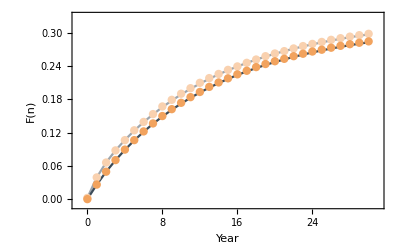

```mathematica
Show[ListPlot[{Partition[Riffle[Table[n,{n,0,31}],F1],2],Partition[Riffle[Table[n,{n,0,31}],F2],2]},PlotRange->{{-1,31},{-0.01,0.33}},Joined->True,Mesh->False,PlotStyle->{Directive[PointSize[0.015],Lighter[RGBColor["#3C4C59"],0.5]],Directive[PointSize[0.015],Lighter[RGBColor["#3C4C59"],0]]}],ListPlot[dataWaitingTimeSelfingCumulativeCross⟦1;;31,{2,3}⟧,PlotRange->{{-1,31},{-0.01,0.33}},PlotStyle->Directive[Lighter[RGBColor["#F2A35E"],0.5],PointSize[0.015],Opacity[1]]],ListPlot[dataWaitingTimeSelfingCumulativeSelf⟦1;;31,{2,3}⟧,PlotRange->{{-1,31},{-0.01,0.33}},PlotStyle->Directive[RGBColor["#F2A35E"],PointSize[0.015],Opacity[1]]],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{"Year","F(n)"}]
```

#### Probability density function of waiting time

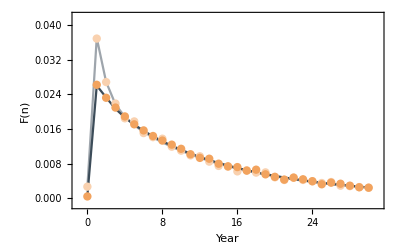

```mathematica
Show[ListPlot[{Partition[Riffle[Table[n,{n,0,31}],P1],2],Partition[Riffle[Table[n,{n,0,31}],P2],2]},PlotRange->{{-1,31},{-.0015,0.042}},Joined->True,Mesh->False,PlotStyle->{Directive[PointSize[0.015],Lighter[RGBColor["#3C4C59"],0.5]],Directive[PointSize[0.015],Lighter[RGBColor["#3C4C59"],0]]}],ListPlot[dataWaitingTimeSelfingCross⟦1;;31,{2,3}⟧,PlotRange->{{-1,31},{-.0015,0.042}},PlotStyle->Directive[Lighter[RGBColor["#F2A35E"],0.5],PointSize[0.015],Opacity[1]]],ListPlot[dataWaitingTimeSelfingSelf⟦1;;31,{2,3}⟧,PlotRange->{{-1,31},{-.0015,0.042}},PlotStyle->Directive[RGBColor["#F2A35E"],PointSize[0.015],Opacity[1]]],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{"Year","F(n)"}]
```